```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["A:\\heap\\180423\\fov_scan\\"]
files = Drop[FileNames[],-1]
prepdat[dataname_,pksel_]:=Module[{dat,dim,pk1, pk2, pk,del,datd,size,minX,minY,datout,fig},
dat=ImportString[StringReplace[Import[dataname, "Text"],{";"->""}],"CSV","HeaderLines"->6];
dim=Dimensions[dat];

pk1=Position[dat,Max[dat]][[1]];
del=RotateRight[DiskMatrix[10,dim],{pk1[[1]]-dim[[1]]/2,pk1[[2]]-dim[[2]]/2}];
datd=(1-del) dat;
pk2=Position[datd,Max[datd]][[1]];
pk=If[pk1[[2]]<pk2[[2]]&&pksel==1||pk1[[2]]>pk2[[2]]&&pksel==0,pk1,pk2];

size=50;
minX=pk[[1]]-size/2;
minY=pk[[2]]-size/2;
datout=dat[[minX;;minX+size-1,minY;;minY+size-1]];
fig=ArrayPlot[dat,Epilog->{EdgeForm[{Thick,Red}],FaceForm[], Rectangle[{minY,dim[[1]]-minX},{minY+size,dim[[1]]-(minX+size)}]}]//Rasterize;
Return[{datout,pk,fig}]
];

r=80;
Rz[n_,m_,r_]:=If[r==0,0,ZernikeR[n,m,r]];
ϕ[x_,y_]:=If[x==0&&y==0,0,ArcTan[x,y]];
zernfit[x_,y_]:=Sum[Sum[A[n,m]Rz[n,m,(x^2+y^2)^(1/2)/r]*If[m<0,Sin[m ϕ[x,y]],Cos[m ϕ[x,y]]],{m,Which[n==4,0,n==3,-1,n==1||n==2,-n],Which[n==4,0,n==3,1,n==1||n==2,n],2}],{n,1,4}];
vars = Flatten[Table[Table[A[n,m],{m,Which[n==4,0,n==3,-1,n==1||n==2,-n],Which[n==4,0,n==3,1,n==1||n==2,n],2}],{n,1,4}],1];

strehl[data_]:=Module[{psize, dat, pkx, dats, datf, datarg, crop, datargc, dattc, fit, fitNoDefTiltRule, fitoutSub,wrms,s,fig},
psize=400;
dat=PadRight[data,{psize,psize}];
pkx=Position[dat,Max[dat]][[1]];
dats=RotateLeft[dat,{pkx[[1]]-1,pkx[[2]]-1}];
datf=InverseFourier[Sqrt[dats]];
datarg=RotateLeft[Arg[datf]/(2Pi),{psize/2,psize/2}];

crop=DiskMatrix[r,psize];
datargc=RotateRight[datarg crop,{psize/2+r,psize/2+r}][[1;;2r,1;;2r]];

dattc=Reap[Do[If[Sqrt[(i-r)^2+(j-r)^2]<r,Sow[{i-r,j-r,datargc[[i,j]]}]],{i,1,2r},{j,1,2r}]][[2,1]];

fit=NonlinearModelFit[dattc,zernfit[x,y] ,vars,{x,y}];

fitNoDefTiltRule = Join[Drop[Drop[fit["BestFitParameters"],2],{2}],{A[1,-1]->0,A[1,1]->0,A[2,0]->0}];
fitoutSub=Reap[Do[If[Sqrt[(i-r)^2+(j-r)^2]<r,Sow[{i-r,j-r,zernfit[i-r,j-r]/.fitNoDefTiltRule}]],{i,1,2r},{j,1,2r}]][[2,1]];
wrms=RootMeanSquare[fitoutSub[[All,3]]];
s=1-(2Pi wrms)^2;

fig=ArrayPlot[datarg,PlotRange->{-1,1},Epilog->{Red,Circle[{psize/2,psize/2},r]}]//Rasterize;

Return[{s,fig}]
];
```

A:\heap\180423\fov_scan

{10.wct,11.wct,12.wct,13.wct,14.wct,15.wct,16.wct,17.wct,1.wct,2.wct,3.wct,4.wct,5.wct,6.wct,7.wct,8.wct,9.wct}

```mathematica
datin0=prepdat[#,0]&/@files;//AbsoluteTiming
Dimensions[datin0]
```

{32.6094,Null}

{17,3}

```mathematica
datin1=prepdat[#,1]&/@files;//AbsoluteTiming
Dimensions[datin1]
```

{31.9076,Null}

{17,3}

```mathematica
sout0=strehl[#]&/@datin0[[All,1]];//AbsoluteTiming
```

Experimental`NumericalFunction::dimsl: {y} given in {x,y} should be a list of dimensions for a particular argument.

General::stop: Further output of Experimental`NumericalFunction::dimsl will be suppressed during this calculation.

{211.773,Null}

```mathematica
sout1=strehl[#]&/@datin1[[All,1]];//AbsoluteTiming
```

Experimental`NumericalFunction::dimsl: {y} given in {x,y} should be a list of dimensions for a particular argument.

General::stop: Further output of Experimental`NumericalFunction::dimsl will be suppressed during this calculation.

{205.635,Null}

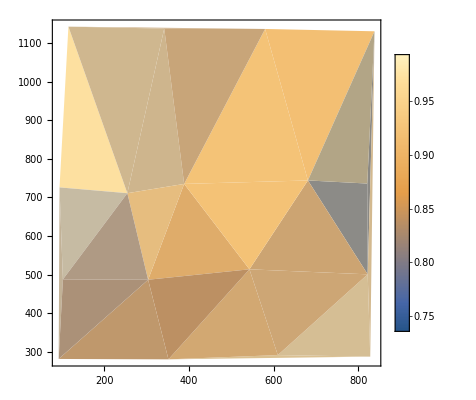

```mathematica
keyVals =ToExpression[ Map[StringSplit[#,"."][[1]]&,files]];
posvals=datin0[[All,2]];
svals=sout0[[All,1]];
ListDensityPlot[Table[{posvals[[i,1]],posvals[[i,2]],svals[[i]]},{i,1,Length[svals]}],PlotLegends->Automatic,InterpolationOrder->1]
```

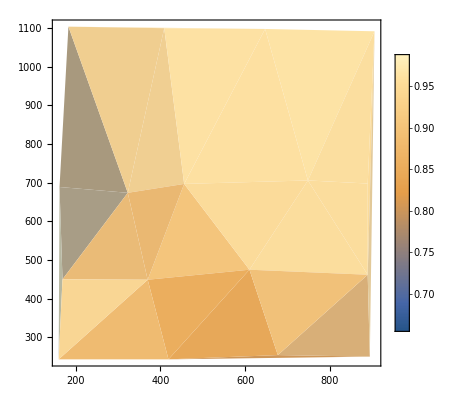

```mathematica
keyVals =ToExpression[ Map[StringSplit[#,"."][[1]]&,files]];
posvals=datin1[[All,2]];
svals=sout1[[All,1]];
ListDensityPlot[Table[{posvals[[i,1]],posvals[[i,2]],svals[[i]]},{i,1,Length[svals]}],PlotLegends->Automatic,InterpolationOrder->1]
```

```mathematica
svals=sout0[[All,1]]
svals=sout1[[All,1]]
```

{0.903705,0.812145,0.956008,0.977773,0.935079,0.872685,0.79179,0.963508,0.950005,0.993031,0.953523,0.944699,0.735957,0.801856,0.86817,0.836658,0.773568}

{0.969137,0.819678,0.816962,0.770046,0.974829,0.921771,0.987825,0.958006,0.806234,0.655156,0.963258,0.982674,0.890907,0.970555,0.889951,0.854372,0.977424}

```mathematica
svals
```

{0.969137,0.819678,0.816962,0.770046,0.974829,0.921771,0.987825,0.958006,0.806234,0.655156,0.963258,0.982674,0.890907,0.970555,0.889951,0.854372,0.977424}

```mathematica
Export["sout85.txt",{"posvals",posvals,"sout_r=85",sout[[All,1]]}]
```

sout130.txt

```mathematica
datin
```

{{{{3829,2151,2446,3845,3746,2566,2566,3073,3210,3351,4427,2927,2396,3384,2645,2064,2516,2221,3164,2695,2118,3791,2998,1432,2803,2496,3334,1756,2383,2687,2944,1636,3139,3102,2620,2944,3359,2163,2566,1756,2404,3235,2944,1935,3438,2699,2936,3754,3795,2014},48,{3683,2280,1561,3139,2832,4389,2583,3285,2487,4531,3368,3260,2591,2375,3484,3251,2321,4377,1486,3376,4439,3372,4007,3359,3276,3326,3438,2795,3401,2774,3064,2666,3866,2288,3384,2595,3646,2566,3542,3413,3089,3451,3064,2799,3779,1885,3405,3114,3405,3052}},{160,243},-Graphics-},{{1},{419,243},-Graphics-},13,{1},{{1},{169,450},-Graphics-}}
 |  |  |  |

```mathematica
sout
```

{{0.9213,-Graphics-},{0.819783,-Graphics-},{0.909771,-Graphics-},{0.838092,-Graphics-},{0.968199,-Graphics-},{0.988118,-Graphics-},{0.989954,-Graphics-},{0.975757,-Graphics-},{0.829042,-Graphics-},{0.66707,-Graphics-},{0.996863,-Graphics-},{0.969824,-Graphics-},{0.965877,-Graphics-},{0.950521,-Graphics-},{0.884503,-Graphics-},{0.958456,-Graphics-},{0.989325,-Graphics-}}